# Jacob Russell

## Numerical Analysis

## Newton Raphson and the Secant Method

```mathematica
newtonRaphson[f_, pX_, tol_, max_]:=Module[{x=N[pX], k=0},
While[k≤max&&Abs[f[x]]>tol,
x=x-f[x]/f'[x];
k++;
];
If[k>max, Print["Maximum number of iterations exceeded."], Return[{x, f[x]}]];
]
```

```mathematica
secant[f_, pX1_,pX2_, tol_, max_]:=Module[{x1=N[pX1], x2=N[pX2], k=0},
While[k≤max&&Abs[f[x1]]>tol,
x1=x1-f[x1]((x1-x2)/(f[x1]-f[x2]));
k++;
];
If[k>max, Print["Maximum number of iterations exceeded."], Return[{x1, f[x1]}]];
]
```

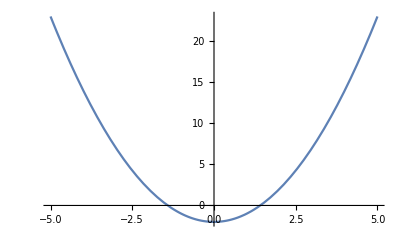

```mathematica
Plot[x^2-2,{x, -5,5}]
```

```mathematica
newtonRaphson[Function[x,x^2-2],2,.001,50]
```

{1.41422,6.0073×10^-6}

```mathematica
secant[Function[x,x^2-2],2,4,.001,50]
```

{1.41451,0.000847624}

## 1)

```mathematica
motion[t_]=9600(1-ⅇ^(-t/15))-480t;
```

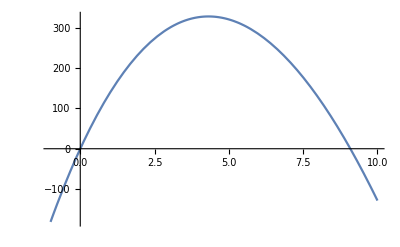

```mathematica
Plot[9600(1-ⅇ^(-t/15))-480t,{t,-1,10}]
```

## a)

```mathematica
newtonRaphson[Function[t,motion[t]], 8, .001, 100]
```

{9.0879,-0.0000317292}

```mathematica
secant[Function[t,motion[t]],7,8,.001,100]
```

{9.08789,0.000633062}

## b)

```mathematica
range[q_]=2400(1-ⅇ^(-q/15));
```

```mathematica
range[9.087894829331287]
```

1090.55

## 2)

```mathematica
poly[p_]=2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4;
```

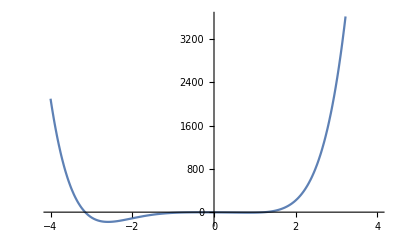

```mathematica
Plot[2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4,{x,-4,4}]
```

```mathematica
newtonRaphson[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],-4,.001,100]
```

{-3.15312,3.78002×10^-9}

```mathematica
secant[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],-4,-3.5,.001,100]
```

{-3.15312,0.00065152}

```mathematica
newtonRaphson[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],1,.001,100]
```

{1.25242,2.54459×10^-7}

```mathematica
secant[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],1,1.5,.001,100]
```

{1.25241,-0.000663195}

```mathematica
secant[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],1+ⅈ,1.5+ⅈ,.001,100000]
```

{-0.448324-0.498446 ⅈ,0.000574357-0.000757275 ⅈ}

```mathematica
newtonRaphson[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],1+ⅈ,.001,100]
```

{-0.448266+0.498444 ⅈ,0.00014947+0.000117683 ⅈ}

```mathematica
secant[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],-2+ⅈ,-2.5+ⅈ,.001,100000]
```

{0.14863+1.05114 ⅈ,0.000751766-0.0006067 ⅈ}

```mathematica
newtonRaphson[Function[x,2 x^6+5 x^5-3 x^4+2 x^3-6 x^2-5x-4],.1+ⅈ,.001,100]
```

{0.148602+1.05116 ⅈ,-0.0000211319-0.0000251676 ⅈ}

## 3)

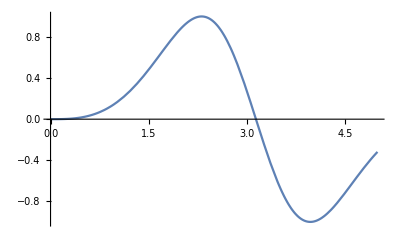

```mathematica
Plot[Sin[x-Sin[x]], {x,0,5}]
```

```mathematica
newtonRaphson[Function[x,Sin[x-Sin[x]]-0.5],2.1,.001,100]
```

```mathematica
{1.5231296563084566,0.0005772864631551355}
(1.5231,0.5)
```